## Section Teoria - Balanço de energia de micropartícula imersa em plasma (Marco Antonio Ridenti, ITA, São José dos Campos, 06/08/2018) Uma partícula microscópica sólida e esférica, imersa em um plasma de temperatura T_p, inicialmente a uma temperatura T_0<T_p sofre um influxo de energia em decorrência da convecção e da radiação do plasma (Plasma Physics and Engineering, Fridman & Kennedy, 2004), e perde energia por irradiação. Em certas condições, a corrente iônica - que gera recombinação de cargas sobre a superfície da partícula - pode transferir energia para a partícula (Int. J. Heat Mass Transfer, Leveroni & Pfender, Vol. 33, No. 7). Esse efeito, no entanto, pode ser levado em consideração corrigindo-se o coeficiente de transferência de calor (α) no termo de convectivo. O balanço de energia pode ser expresso como (Fridman & Kennedy, 2004) c_p ϱ 4/3 π r_a^3 (∂T)/(∂t)= π pE r_a^2+4π r_a^2 λ(∂T)/(∂r)-4π r_a^2 σ T^4 (1.1) onde c_p é a o calor específico a pressão constante da partícula, ϱ é a sua densidade, r_a seu raio, pE o fluxo de energia de fótons, em W/m^2, λ o coeficiente térmico do plasma e σ a constante de Stefan-Boltzmann. O primeiro termo do lado esquerdo da equação representa a taxa de variação de calor da partícula. O primeiro, segundo e terceiro termos do lado direito da equação são, respectivamente, o ganho de energia por influxo de fótons, fluxo de calor e a perda por radiação de corpo negro. Essa expresão pode ser simplificada, introduzindo-se agora o coeficiente de transferência de calor (α) , (∂T)/(∂t)= -a T^4 - b (T- T_p)+c (1.2) onde a,b e c são definidos como a =σ/(c_p ϱ L) ; b =α/(c_p ϱ L) ; c=pE/(4 c_p ϱ L) (1.3) e L é a dimensão caracterísitca da partícula definida como L=r_a/3. Nosso problema se reduz a resolver a equação (1.2) para verificar se a partícula adquire a temperatura de equilíbrio no tempo típico de trânsito na tocha. Vários parâmetros precisam ser estimados para obter a solução de (1.2). Um dos parâmetros críticos é o coeficiente de transferência de calor. O método mais simples simples utiliza a equação de Ranz-Marshall, Nu= 2.0 + 0.6*Re^0.5 Pr^0.33 (1.4) onde Nu é o número de Nusselt, Re é o número de Reynolds e Pr é o número de Prandtl. Essas grandezas adimensionais são definidas como Nu =(α L)/λ ; Re =u/(ν L) ; Pr=(c_(p,g)μ)/λ (1.5) onde ν e μ são as viscosidades cinemática e dinâmica, respectivamente, e c_(p,g) é o calor específico do gás. A expressão (1.4) é válida para micropartículas imersas em um gás quente convencional (High Temp. Material Processes, Vol. 1, Vardelle et al, 1997). Outros efeitos podem entrar em jogo, tal como variações das propriedades do gás na camada limite ou efeitos não contínuos no caso de partículas subnanométricas (Int. J. Heat Mass Transfer, Leveroni & Pfender, Vol. 33, No. 7). O cálculo da evolução da temperatura considera que a transferência de calor ocorre sobretudo dentro da tocha, quando as partículas se deslocam através da câmara de mistura. -Graphics-

```mathematica
centPixels = {579.667,544.681};
bordPixels = {687.257,654.467};
diffPixels = bordPixels-centPixels;
pixelValue =Sqrt[Dot[diffPixels,diffPixels]];
convFactor = 0.03/pixelValue;
firstPath = (941.959-579.667)*convFactor
secondPath = (579.667 - 85.6326)*convFactor
radiusA = (450.266 - 395.373)*convFactor/2
```

0.0707068

0.0964183

0.0053566

## Na câmara de mistura a pressão é elevada, da ordem de 2 a 3 bars, e a partir do bocal de saída ocorre a expansão supersônica. Para interpretar a solução da equação (1.2), é necessário estimar o tempo de trânsito da partícula através da câmara de mistura. Para estimar o tempo de trânsito, vamos considerar que a velocidade de fluxo do gás é constante até o centro da trajetória, e igual a v_1=Q_1/A, onde Q_1 é o fluxo de entrada do gás e A é a seção tranversal do tubo, e que a partir do centro a velocidade passa a ser dada por v_2=(Q_1+Q_2)/A. No primeiro trecho, vamos considerar que a partícula - independentemente do tamanho - já atingiu a velocidade terminal igual à do fluxo do gás, isto é v_1=Q_1/A=60 [SLM]/(π*0.005^2)[m^2]=12.73 m/s (1.6) Δt_1=Δx_1/v_1=0.0055s (1.7)

```mathematica
min2sec = 60;
l2m3 = 0.001; 
vel1 = (60*l2m3/min2sec)/(Pi*Power[0.005,2])  
deltat1 = firstPath/vel1
```

12.7324

0.0055533

Na estimativa mais simplista, podemos considerar que as particulas atingem instantaneamente uma velocidade terminal igual à velocidade de fluxo v_2 no segundo trecho da trajetória. Deste modo, temos  
v_2=(Q_1+Q_2)/A=(250 [SLM]+60 [SLM])/(π*0.005^2)[m^2]=65.78 m/s 	(1.8)
Δt_2=Δx_2/v_2=0.0015s	(1.9)
Δt=Δt_1+Δt_2=0.0070s	(1.10)

```mathematica
vel2 = ((60+250)*l2m3/min2sec)/(Pi*Power[0.005,2])  
deltat2 = secondPath/vel2
deltat = deltat1+deltat2
```

65.784

0.00146568

0.00701898

Nossa estimativa para o tempo total de trânsito é 7 ms. A estimativa é grosseira, e provavelmente superestimada, mas em ordem de grandeza é confiável. Na melhor das hipóteses, o tempo total é igual a 2 Δt_2=3 ms.  Mas não é possível um tempo de trânsito inferior a 3 ms.

 código abaixo implementa uma solução numérica da equação (1.2), para partículas de diversos raios, desde 7 μm até 22 μm. Ao final, é apresentado o gráfico das soluções. Verifica-se que as partículas atingem o equilíbrio em todos os casos para um intervalo de 3 ms. As particulas menores atingem o equilíbrio muito mais rapidamente, como é de se esperar.  À rigor, as temperatura de equilíbrio são um pouco inferiores à temperatura do plasma, em decorrência da perda por irradiação. No pior dos casos, quando o raio é igual a 22 μm, a diferença é de 2% apenas. Nos outros casos essa diferença é ainda menor.  Note-se também que a contribuição do fluxo de fótons para o aquecimento da partícula é desprezível, de modo que o balanço de energia é controlado essencialmente pela transferência de calor por convecção e pela perda radiativa por radiação de corpo negro.

147557.

86075.

60758.8

46950.

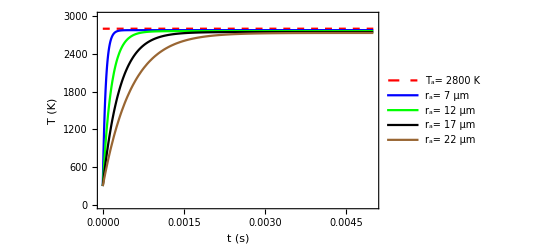

```mathematica
(* --------------------------------------------------------------- *)
(* Functions Definitions *)
restylePlot2[p_,op:OptionsPattern[ListLinePlot]]:=ListLinePlot[Cases[Normal@p,Line[x__]:>x,∞],op,Options[p]]
(* --------------------------------------------------------------- *)
Rg = 8.3144598 ;(* Constante universal dos gases no SI *)
Tp = 2800; (* Plasma temperature in K *)
T0 = 300; (* Initial temperature in K *)
ptor = 2.5*10^5; (*pressure in Pa *)
pinfty = 1*10^5; (* external pressure *)
sigma = 5.670367*(10^(-8)); (* Stefan Boltzmann constant *)
Mzr = 123.2228; (* Molecular mass of Zirconia (g/mol) *)
MN2 = 28; (* Molecular mass of Nitrogen (g/mol) *)
cp = 1000 * 70/Mzr ;(* Specific Heat at constant pressure (J kg-1 K-1) - Thermochimica Acta 403 (2003) 267–273 *)
(* Density values from Royal Society of Chemistry *)
rhom = 5.83*10^3; (* monoclinic zirconia (< 1440 ) *)
rhot = 6.10*10^3; (* tetragonal zirconia (< 2640) *)
rhoc = 6.09*10^3; (* cubic zirconia *)
Ncurves = 4;
rarray= Array[# &, Ncurves, {7*10^(-6), 22*10^(-6 )} ];
crl = Array[# &, 1];
crv = Array[# &, Ncurves];
crvOut = Array[# &, Ncurves];
For[ i=1,i <= Ncurves, i++,
ra = rarray[[i]]; (* Particle Size *)
(* alpha = 5.90 *(10055.06/(3600*(0.3048)^2*5/9)); *) (* 4.52-5.90 - Maximum heat tranfer from Ind.Eng.Chem.Process
Des.Develop.,Vol.10,No.1,1971 *)
(* --------------------------------------------------------------- *)
(* Ranz-Marshall expression for Nusselt Number *)
(* --------------------------------------------------------------- *)
A = 2.0;
B = 0.6;
n = 0.5;
m = 0.3333;
u = 0.0; (* plasma-particle relative speed in m/s  *)
L =  ra/3; (* characteristic dimension *)
mu = 9.1963*10^(-5) ;(* Nitrogen viscosity at Tp, from CEA *) 
k =  0.17215; (* Nitrogen thermal conductivity at Tp *)
cpN2 = 1316.9; (* Nitrogen heat coefficient at constant pressure at Tp *) 
rhoNit = ptor*(MN2*0.0001)/(Rg*Tp); 
nu = mu/rhoNit;(* Nitrogen kinematic viscosity *)
Rey =  u*L/nu; (* Reynolds Number *)
Pr = cpN2*mu/k ; (* Prandtl Number *)
Nu = A + B*Rey^n*Pr^m;
alpha = Nu*k/L;
Print[alpha];
(* --------------------------------------------------------------- *)
pE = 4*Pi*10^(8)*L; (* epsilon ~ 10^8 W/m3/sr Very conservative estimate from data in book Thermal Plasmas, for nitrogen plasma, at 100kPa with Fe particles, Boulos, Fauchais and Pfender *)
a = sigma/(cp*rhoc*L) ;(* Stefan-Boltzmann term coefficient *)
b = alpha/(cp*rhoc*L);(* Convection term coefficient *)
c = pE/(4*cp*rhoc*L) ;(* Iradiance heating, roughly estimated *)
t0 = 0; (* Initial time *)
tf = 0.005; (* Final time in seconds *)
model = {y'[t] == -a*y[t]^4-b*(y[t]-Tp)+c, y[0] == T0};
s = NDSolve[model, y, {t,t0, tf}];
crv[[i]] = Plot[Evaluate[y[t] /. s], {t, t0, tf},AxesLabel -> { "t (s)","T (K)"},  PlotStyle -> {Blue}, PlotRange -> {0, 5000}];
]
crl= Plot[Tp, {t,t0,tf}, PlotStyle -> {Red,Dashed}];
restylePlot2[{crl,crv}, PlotStyle -> {{Red, Dashed},{Blue},{Green}, {Black}, {Brown}}, Joined->True,FrameLabel -> { "t (s)","T (K)"}, Frame -> True, PlotRange -> {{0,tf},{0, 3000}}, PlotLegends -> {"T_a= 2800 K","r_a= 7 μm","r_a= 12 μm","r_a= 17 μm","r_a= 22 μm"}]
```